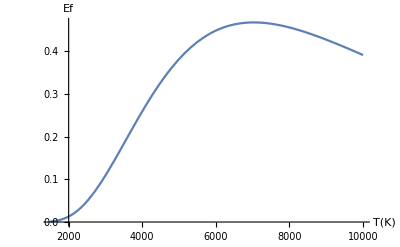

```mathematica
h=6.62606957 10^-34;
c=299792458.0;
k=1.3806488 10^-23;
V[l_,t_]:=(1/(l^5))*(1/(Exp[h*c/(k*t*l)]-1));
a[t_]:=NIntegrate[V[l,t],{l,0,20}];
b[t_]:=NIntegrate[V[l,t],{l,380 10^-9,750 10^-9}]
coiso[t_]:=(b[t])/a[t]

Plot[coiso[t],{t,1500,10000},AxesLabel->{HoldForm[T[K]],HoldForm[Ef]}]
```

```mathematica
Plot
```

```mathematica
coiso[1886]
```

0.0084168